```mathematica
t1a=0;t1r=0; cc=buildCC2D[{{1}}];
{numPT,pt,ct,kft,oit,olt,isE}=getNumParent[cc];
iso=startIsoTable[pt,cc];
iso
```

{{Null,Null,Null,Null},{Null,Null,Null,Null},{0}}

```mathematica
kthIter=1;
{kft,spNum,spPairs}=updateDisjoint[numPT,kft,ct,isE,cc];
spNum
spPairs
```

1

{{{3,1},{2,1}}}

```mathematica
kft
```

{{False,False,False,False},{True,False,False,False},{True}}

```mathematica
{kft,isE2,spNum}=oneCellExclusionTest2[kft,iso,isE,pt,kthIter,t1a,t1r,spNum,spPairs];
```

```mathematica
kft
```

{{False,False,False,False},{True,False,False,False},{True}}

```mathematica
spNum
```

1

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
numPT
pt
ct
```

{{1,1,2,2},{0,0,0,0},{0}}

{{{4},{2},{2,3},{3,4}},{{},{},{},{}},{{}}}

{{{},{},{},{}},{{},{2,3},{3,4},{4,1}},{{}}}

```mathematica
iso=setIsoTable[pt,kthIter,iso,cc];
iso
```

{{Null,Null,Null,Null},{1,1,1,1},{0}}

```mathematica
kthIter++;
kthIter
```

2

```mathematica
{kft1,spNum1,spPairs2}=updateDisjoint[numPT,kft,ct,isE2,cc];
kft1
spNum1
spPairs2
```

{{True,True,False,False},{True,True,False,True},{True}}

2

{{{2,2},{1,2}},{{2,4},{1,1}}}

```mathematica
isE2
```

{{False,False,False,False},{False,False,False,False},{False}}

```mathematica
numPT
```

{{1,1,2,2},{0,0,0,0},{0}}

```mathematica
pt
```

{{{4},{2},{2,3},{3,4}},{{},{},{},{}},{{}}}

```mathematica
iso
```

{{Null,Null,Null,Null},{1,1,1,1},{0}}

```mathematica
ct
```

{{{},{},{},{}},{{},{2,3},{3,4},{4,1}},{{}}}

```mathematica
{kft2,isE3,spNum2}=oneCellExclusionTest2[kft1,iso,isE2,pt,kthIter,t1a,t1r,spNum1,spPairs2];
kft2
spNum2
isE3
```

{{False,False,False,False},{True,False,False,False},{True}}

0

{{True,True,False,False},{False,True,False,True},{False}}

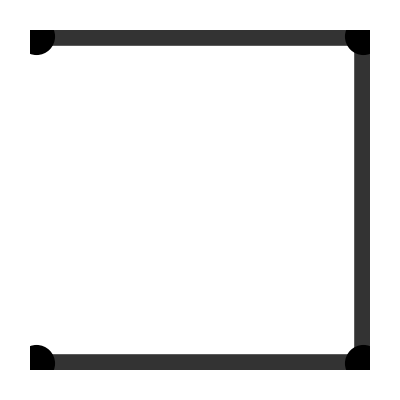

```mathematica
showCC2D[thin[cc,{{t1a,t1r}}]]
```

```mathematica
Length[Position[Map[#⟦1⟧&,{{3,1},{4,1}}],3]]
```

1